```mathematica
ClearAll["Global`*"];
```

```mathematica
sol=y[s]/.First[NDSolve[{y''[s]==-1+y'[s]^2,y[0]==1,y'[0]==0},y,{s,0,Infinity},Method->{"EventLocator","Event":>y[s],"EventAction":>Throw[tend=s,"StopIntegration"]}]]
tend
```

InterpolatingFunction[{{0.,1.65745}},<>][s]

1.65745

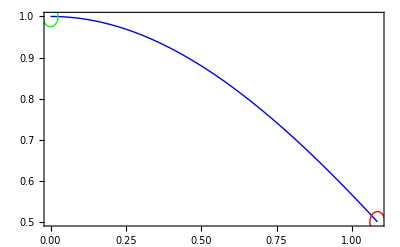

```mathematica
plt=Plot[sol,{s,0,tend},Frame->True,Axes->False,PlotStyle->Blue,DisplayFunction->Identity];
grp=Graphics[{{Green,Circle[{0,1},0.025]},{Red,Circle[{tend,sol/.s->tend},0.025]}}];
Show[plt,grp,DisplayFunction->$DisplayFunction]
```

{{x→InterpolatingFunction[{{0.,0.21598}},<>],y→InterpolatingFunction[{{0.,0.21598}},<>]}}

-0.793692

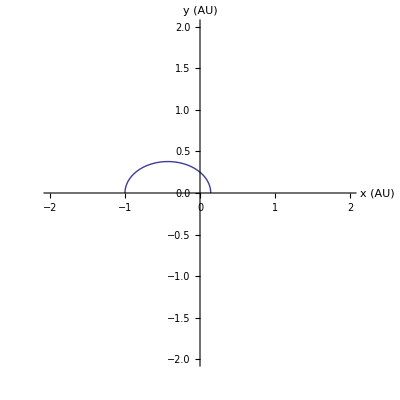

```mathematica
x0 = -1; y0 = 0; x0p = 0; y0p =Pi; tf = 0.5;
Aorbit=NDSolve[{x''[t]+(4 Pi^2) x[t]/(x[t]^2+y[t]^2)^(3/2)==0,
y''[t]+(4 Pi^2) y[t]/(x[t]^2+y[t]^2)^(3/2)==0,
x[0]==x0,y[0]==y0,
x'[0]==x0p,y'[0]==y0p},
{x,y},{t,0,tf},
Method->{"EventLocator","Event":>y[t]<0,"EventAction":>Throw[tend=t,"StopIntegration"]}]
x[0.1] /. Aorbit[[1]][[1]]
ParametricPlot[Evaluate[{x[t],y[t]}/.Aorbit],{t,0,tend},AxesLabel->{"x (AU)"," y (AU)"}, PlotRange -> {{-2,2},{-2,2}}]
```